## Canonicity factors

Creating proper inertia factors A_2 and A_3 from the value of A_1

```mathematica
ClearAll["Global`*"]
```

```mathematica
T[j_,gm_]:=1/(j(j+1))√3(√3 Cos[gm]+Sin[gm]);
TP[j_,gm_]:=1/(j(j+1))2 √3 Sin[gm];
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-1-2I)/(2j-1);
```

```mathematica
A3condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*T[j,gm]);
A2condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*TP[j,gm]);
```

```mathematica
A1=0.1;
I0=35/2;
j0=13/2;
V0=3;
gm0=25;
A2test1[I_,j_]:=Abs[A2condition[A1,I,j,V0,gm0*π/180]];
A3test1[I_,j_]:=Abs[A3condition[A1,I,j,V0,gm0*π/180]];
A2test2[I_,j_]:=Abs[A3condition[A1,I,j,V0,gm0*π/180]];
A3test2[I_,j_]:=Abs[A2condition[A1,I,j,V0,gm0*π/180]];
```

```mathematica
k1[I_,j_,A1_,A2_,A3_]:=(I^2*((2I-1)(A2-A1)+2j*A1)/((2I-1)(A3-A1)+2j*A1))^(1/4);
(*k1[35/2,j0,A1,A2test1[35/2,j0],A3test1[35/2,j0]]
k1[35/2,j0,A1,A2test2[35/2,j0],A3test2[35/2,j0]]*)
(*A2test1[35/2,j0]
A3test1[35/2,j0]
A2test2[35/2,j0]
A3test2[35/2,j0]*)
```

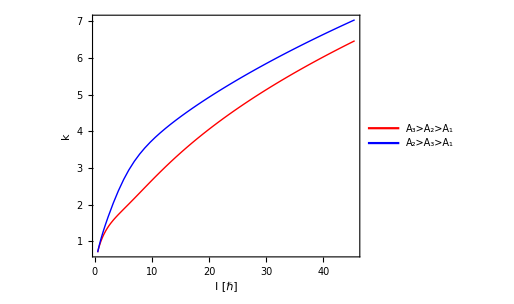

```mathematica
Plot[{k1[x,j0,A1,A2test1[x,j0],A3test1[x,j0]],k1[x,j0,A1,A2test2[x,j0],A3test2[x,j0]]},{x,0.5,45.5},AspectRatio->0.8,Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full,FrameLabel->{"I [ℏ]","k"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->380,PlotLegends->Placed[{"A_3>A_2>A_1","A_2>A_3>A_1"},{0.75,0.3}]]
```